ⅇ^-s/(√π)

(ⅇ^(-s/2) (2-s))/(4 √(2 π))

(ⅇ^(-s/2) s)/(4 π)

(ⅇ^(-s/3) (27-18 s+2 s^2))/(81 √(3 π))

1/81 ⅇ^(-s/3) (6-s) s

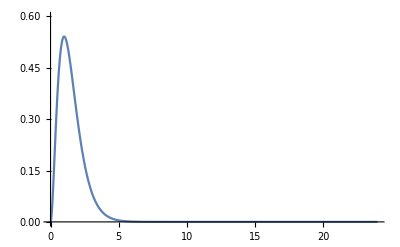

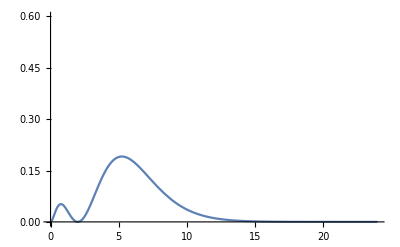

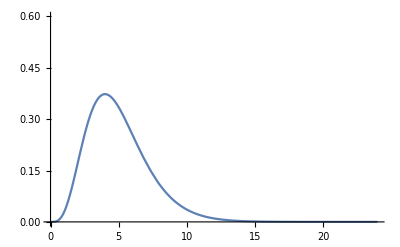

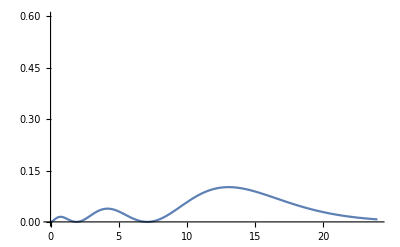

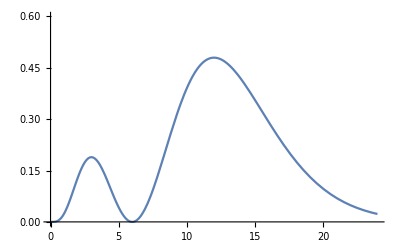

```mathematica
a=1;Z=1;
o1s[s_]=1/Sqrt[Pi]*(Z/a)^(3/2)*Exp[-s]
o2s[s_]=1/4/Sqrt[2*Pi]*(Z/a)^(3/2)*(2-s)*Exp[-s/2]
o2p[s_]=1/4/Sqrt[2*Pi]*(Z/a)^(3/2)*s*Exp[-s/2]*Sqrt[2/Pi]
o3s[s_]=1/81/Sqrt[3*Pi]*(Z/a)^(3/2)*(27-18*s+2*s^2)*Exp[-s/3]
o3p[s_]=1/81*(Z/a)^(3/2)*(6-s)*s*Exp[-s/3]

Plot[4*Pi*s*s*o1s[s]^2,{s,0,24},PlotRange->{0,0.6}]
Plot[4*Pi*s*s*o2s[s]^2,{s,0,24},PlotRange->{0,0.6}]
Plot[4*Pi*s*s*o2p[s]^2,{s,0,24},PlotRange->{0,0.6}]
Plot[4*Pi*s*s*o3s[s]^2,{s,0,24},PlotRange->{0,0.6}]
Plot[4*Pi*s*s*o3p[s]^2,{s,0,24},PlotRange->{0,0.6}]
```

```mathematica
o2px[x_,y_,z_]=1/4/Sqrt[2*Pi]*(Z/a)^(3/2)*x*Exp[-Sqrt[x^2+y^2+z^2]/2]
o2py[x_,y_,z_]=1/4/Sqrt[2*Pi]*(Z/a)^(3/2)*y*Exp[-Sqrt[x^2+y^2+z^2]/2]
o2pz[x_,y_,z_]=1/4/Sqrt[2*Pi]*(Z/a)^(3/2)*z*Exp[-Sqrt[x^2+y^2+z^2]/2]
ContourPlot3D[o2s[Sqrt[x^2+y^2+z^2]],{x,-7,7},{y,-7,7},{z,-7,7},PlotTheme->"Business",AxesLabel->Automatic]
ContourPlot3D[o2px[x,y,z],{x,-7,7},{y,-7,7},{z,-7,7},PlotTheme->"Business",AxesLabel->Automatic]
ContourPlot3D[o2py[x,y,z],{x,-7,7},{y,-7,7},{z,-7,7},PlotTheme->"Business",AxesLabel->Automatic]
ContourPlot3D[o2pz[x,y,z],{x,-7,7},{y,-7,7},{z,-7,7},PlotTheme->"Business",AxesLabel->Automatic]
```

(ⅇ^(-1/2 √(x^2+y^2+z^2)) x)/(4 √(2 π))

(ⅇ^(-1/2 √(x^2+y^2+z^2)) y)/(4 √(2 π))

(ⅇ^(-1/2 √(x^2+y^2+z^2)) z)/(4 √(2 π))

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

```mathematica
ContourPlot3D[o2s[Sqrt[x^2+y^2+z^2]]/Sqrt[2]+o2px[x,y,z]/Sqrt[2],{x,-10,10},{y,-10,10},{z,-10,10},PlotTheme->"Business",AxesLabel->Automatic]
ContourPlot3D[o2s[Sqrt[x^2+y^2+z^2]]/Sqrt[3]+o2px[x,y,z]*Sqrt[2/3],{x,-10,10},{y,-10,10},{z,-10,10},PlotTheme->"Business",AxesLabel->Automatic]
ContourPlot3D[o2s[Sqrt[x^2+y^2+z^2]]/2+o2px[x,y,z]/2+o2py[x,y,z]/2+o2pz[x,y,z]/2,{x,-10,10},{y,-10,10},{z,-10,10},PlotTheme->"Business",AxesLabel->Automatic]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-